```mathematica
nb1=NotebookOpen["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures/Ratesfunc.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
StarRates={Rstar,Hstar,Fstar}/.{λ->Growth,μ->Mortality,m->Maintenance,α->Resourcegrowth,σ->Starvation,ρ->Recovery};
```

Energy equivalence hypothesis

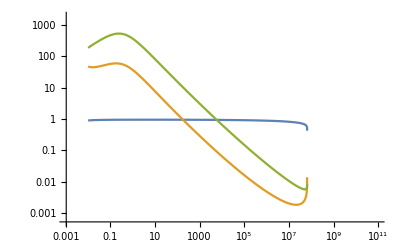

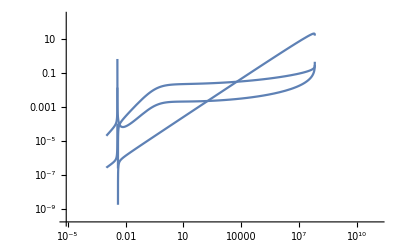

```mathematica
LogLogPlot[StarRates,{M,.01,10^10}]
LogLogPlot[StarRates*Maintenance,{M,.0001,10^10}]
```

Viable for an Rstar Argument

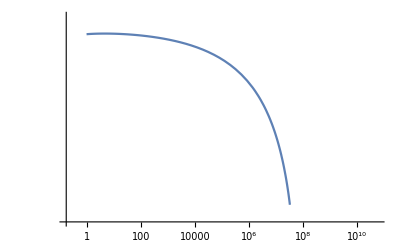

```mathematica
LogLogPlot[StarRates[[1]],{M,1,10^10}]
```